# Play around with replace

## Load data

```mathematica
<<HokahokaW`
```

HokahokaW`
Git HEAD hash loaded on Mon 11 May 2015 20:18:03 is dfc276416b3fda60a30e53692c8c82eaed59709c.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

```mathematica
testFileName=ParentDirectory[NotebookDirectory[]]<>"\\_resources\\tDC004_150313_120455.pp2rl.tsv"
```

C:\prog\_lab\pyonpyon\pyonpyonw\Tests\_resources\tDC004_150313_120455.pp2rl.tsv

```mathematica
testData=Import[testFileName]
```

{{DAQCONFIG MEMO,Shock intensity AO,Code_LED DO,Switch DI,Webcam,AO <=> Sound card,Sound card,Subject Name,sample rate,Variable shock,Log File Directory,Webcam on,Tone gate PFI},{DAQCONFIG,Dev3/ao0,Dev3/ao1,Dev3/port0,Dev3/port2/line0,cam9,FALSE,0,100000.,TRUE,TRUE,/Dev3/PFI0},{SESSPARAM MEMO,Log File Directory Root,Habit tr0 (s),ITI max (s),ITI min (s),Tone repeat (ms),Jump time (s),Subject Name,Start trial,Stay (s),Log File Directory,Pre click (V),Click del (s)},{SESSPARAM,E:\Data\tDC.Coulb1,180,24,14,0,4,tDC004,0,5,E:\Data\tDC.Coulb1\tDC004\150313\120455,0.1,1.},{TRIALMEMO,Trial Type Number,Trial Type,Trial Weight,Shock (mA),Duration (ms),Sound Type,Stim P1,Stim P2,Stim P3,Stim P4},{STATE MEMO,Curr tr,Cum (ms),Run loop diff,Trial Type Number,Curr State,Null,Sw,Tone Gate,Stim,Current DAQ DO Int,Last dur jump time memo (ms),Last dur shock time memo (ms)},{RUNLOG,PCR6985-17,pyonpyon2.vi,1225},{STATE,0,21,21,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,4925,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,51182,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,79973,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,99263,3,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,120476,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,144788,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,168337,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,180016,9,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    77},{STATE,0,180093,77,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,0,181015,8,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    65},{STATE,0,186082,65,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,0,187085,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,0,191295,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,203},{STATE,0,191307,12,1,14,FALSE,TRUE,FALSE,FALSE,484,0,203},{STATE,1,207073,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    57},{STATE,1,207130,57,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,1,211255,3,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    26},{STATE,1,216282,26,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,1,216413,15,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{STATE,1,217285,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,1,218378,4,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,1,218383,5,1,6,FALSE,FALSE,TRUE,FALSE,354,1096,0},{STATE,1,218387,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1096,0},{STATE,1,218397,10,1,14,FALSE,FALSE,FALSE,FALSE,480,1096,0},{STATE,1,221045,4,1,14,FALSE,TRUE,FALSE,FALSE,484,1096,0},{STATE,1,229682,4,1,14,FALSE,FALSE,FALSE,FALSE,480,1096,0},{STATE,1,234820,2,1,14,FALSE,TRUE,FALSE,FALSE,484,1096,0},{STATE,2,237824,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    48},{STATE,2,237872,48,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    69},{STATE,2,242941,69,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,2,243944,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,2,245003,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,2,245011,8,1,6,FALSE,FALSE,TRUE,FALSE,354,1062,0},{STATE,2,245015,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1062,0},{STATE,2,245026,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0},{STATE,2,249728,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1062,0},{STATE,2,266035,3,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0},{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    55},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    38},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,4,300445,2,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    54},{STATE,4,300499,54,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,4,304774,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    37},{STATE,4,309813,37,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,4,310817,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,4,314821,3,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,4,314825,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,4,314835,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,5,336458,4,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    63},{STATE,5,336521,63,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,5,340651,3,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,5,343307,4,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    45},{STATE,5,348355,45,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,5,349360,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,5,353365,3,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,5,353369,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,5,353379,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,6,372431,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    69},{STATE,6,372500,69,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,6,373304,3,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    38},{STATE,6,378346,38,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,6,379349,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,6,381341,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,6,381347,6,1,6,FALSE,TRUE,TRUE,FALSE,358,1995,0},{STATE,6,381351,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1995,0},{STATE,6,381361,10,1,14,FALSE,TRUE,FALSE,FALSE,484,1995,0},{STATE,6,389729,4,1,14,FALSE,FALSE,FALSE,FALSE,480,1995,0},{STATE,6,395192,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1995,0},{STATE,7,402238,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    57},{STATE,7,402295,57,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    34},{STATE,7,407330,34,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,7,408335,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,7,412339,2,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,7,412343,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,7,412353,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,8,430808,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    43},{STATE,8,430851,43,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    55},{STATE,8,435906,55,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,8,436915,9,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,8,438257,4,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,8,438263,6,1,6,FALSE,FALSE,TRUE,FALSE,354,1351,0},{STATE,8,438267,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1351,0},{STATE,8,438278,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1351,0},{STATE,8,445489,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1351,0},{STATE,9,454346,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    43},{STATE,9,454389,43,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,9,458881,2,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    46},{STATE,9,463929,46,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,9,464933,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,9,466058,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,9,466064,6,2,9,FALSE,TRUE,TRUE,TRUE,663,1128,0},{STATE,9,469067,3,2,9,FALSE,FALSE,TRUE,TRUE,659,1128,0},{STATE,9,469073,6,2,14,FALSE,FALSE,TRUE,FALSE,738,1128,3009},{STATE,9,469083,10,2,14,FALSE,FALSE,FALSE,FALSE,736,1128,3009},{STATE,10,491936,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    39},{STATE,10,491975,39,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    59},{STATE,10,497035,59,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,10,498040,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,10,498113,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,10,498119,6,1,6,FALSE,TRUE,TRUE,FALSE,358,76,0},{STATE,10,498123,4,1,14,FALSE,TRUE,TRUE,FALSE,486,76,0},{ERROR,99999,Run loop diff is >25 ms:    187},{STATE,10,498310,187,1,14,FALSE,TRUE,FALSE,FALSE,484,76,0},{STATE,10,498794,4,1,14,FALSE,FALSE,FALSE,FALSE,480,76,0},{STATE,10,506846,3,1,14,FALSE,TRUE,FALSE,FALSE,484,76,0},{STATE,11,521999,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    54},{STATE,11,522053,54,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,11,522584,3,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    44},{STATE,11,527629,44,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,11,528632,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,11,532637,3,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,11,532641,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,11,532651,10,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,11,535592,4,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,12,550832,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    59},{STATE,12,550891,59,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    54},{STATE,12,555947,54,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,12,556951,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,12,560956,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,12,561261,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,12,561267,6,1,14,FALSE,FALSE,TRUE,FALSE,482,0,308},{STATE,12,561277,10,1,14,FALSE,FALSE,FALSE,FALSE,480,0,308},{STATE,13,584017,7,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    54},{STATE,13,584071,54,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    26},{STATE,13,589098,26,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,13,590102,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,13,591896,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,13,591908,12,1,6,FALSE,TRUE,TRUE,FALSE,358,1797,0},{STATE,13,591912,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1797,0},{STATE,13,591921,9,1,14,FALSE,TRUE,FALSE,FALSE,484,1797,0},{STATE,13,596852,4,1,14,FALSE,FALSE,FALSE,FALSE,480,1797,0},{STATE,14,612410,4,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    79},{STATE,14,612489,79,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    32},{STATE,14,617521,32,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,14,618526,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,14,622531,3,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,14,622535,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,14,622546,11,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,14,626093,3,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,14,644687,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,15,646421,4,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,15,646451,30,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    69},{STATE,15,651520,69,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,15,651578,3,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{STATE,15,652525,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,15,656527,2,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,15,657195,2,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,15,657201,6,1,14,FALSE,FALSE,TRUE,FALSE,482,0,670},{STATE,15,657213,12,1,14,FALSE,FALSE,FALSE,FALSE,480,0,670},{STATE,16,679034,4,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    63},{STATE,16,679097,63,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    54},{STATE,16,684152,54,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,16,684830,3,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,16,685156,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,16,689162,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,16,689166,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,16,689176,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,16,689620,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,17,705671,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,17,705701,30,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    34},{STATE,17,710736,34,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,17,711739,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,17,713143,2,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,17,713149,6,1,6,FALSE,TRUE,TRUE,FALSE,358,1407,0},{STATE,17,713153,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1407,0},{STATE,17,713163,10,1,14,FALSE,TRUE,FALSE,FALSE,484,1407,0},{STATE,17,717256,2,1,14,FALSE,FALSE,FALSE,FALSE,480,1407,0},{STATE,18,735611,6,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    76},{STATE,18,735687,76,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    49},{STATE,18,740736,49,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,18,741739,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,18,742709,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,18,742714,5,1,6,FALSE,TRUE,TRUE,FALSE,358,973,0},{STATE,18,742718,4,1,14,FALSE,TRUE,TRUE,FALSE,486,973,0},{STATE,18,742729,11,1,14,FALSE,TRUE,FALSE,FALSE,484,973,0},{STATE,18,753713,3,1,14,FALSE,FALSE,FALSE,FALSE,480,973,0},{STATE,19,759829,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    31},{STATE,19,759860,31,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    45},{STATE,19,764905,45,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,19,765911,4,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,19,767311,2,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,19,767317,6,2,9,FALSE,TRUE,TRUE,TRUE,663,1404,0},{STATE,19,769922,1,2,9,FALSE,FALSE,TRUE,TRUE,659,1404,0},{STATE,19,769928,6,2,14,FALSE,FALSE,TRUE,FALSE,738,1404,2611},{STATE,19,769938,10,2,14,FALSE,FALSE,FALSE,FALSE,736,1404,2611},{STATE,20,793118,10,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    73},{STATE,20,793191,73,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    55},{STATE,20,798248,55,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,20,799252,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,20,801872,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,20,801878,6,1,6,FALSE,TRUE,TRUE,FALSE,358,2623,0},{STATE,20,801881,3,1,14,FALSE,TRUE,TRUE,FALSE,486,2623,0},{STATE,20,801892,11,1,14,FALSE,TRUE,FALSE,FALSE,484,2623,0},{STATE,20,816817,11,1,14,FALSE,FALSE,FALSE,FALSE,480,2623,0},{STATE,21,818752,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    35},{STATE,21,818787,35,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    81},{STATE,21,823870,81,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,21,824876,4,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,21,828880,2,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,21,828884,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,21,828895,11,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,22,848140,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    59},{STATE,22,848199,59,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    44},{STATE,22,853246,44,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,22,854252,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,22,856643,4,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,22,856649,6,1,6,FALSE,FALSE,TRUE,FALSE,354,2394,0},{STATE,22,856653,4,1,14,FALSE,FALSE,TRUE,FALSE,482,2394,0},{STATE,22,856664,11,1,14,FALSE,FALSE,FALSE,FALSE,480,2394,0},{STATE,22,863290,3,1,14,FALSE,TRUE,FALSE,FALSE,484,2394,0},{STATE,22,869141,3,1,14,FALSE,FALSE,FALSE,FALSE,480,2394,0},{STATE,23,871021,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    73},{STATE,23,871094,73,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    58},{STATE,23,876152,58,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,23,877156,2,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,23,880541,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,23,880546,5,2,9,FALSE,TRUE,TRUE,TRUE,663,3387,0},{STATE,23,886548,2,2,14,FALSE,TRUE,TRUE,FALSE,742,3387,6005},{STATE,23,886558,10,2,14,FALSE,TRUE,FALSE,FALSE,740,3387,6005},{STATE,23,888232,3,2,14,FALSE,FALSE,FALSE,FALSE,736,3387,6005},{STATE,24,901720,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,24,901750,30,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,24,906779,28,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,24,907783,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,24,911789,4,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,24,911793,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,24,911804,11,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,25,926212,8,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    73},{STATE,25,926285,73,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    58},{STATE,25,931343,58,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,25,932348,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,25,936353,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,25,936960,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,25,936965,5,1,14,FALSE,TRUE,TRUE,FALSE,486,0,610},{STATE,25,936975,10,1,14,FALSE,TRUE,FALSE,FALSE,484,0,610},{STATE,26,951409,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    33},{STATE,26,951442,33,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    58},{STATE,26,956501,58,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,26,957508,5,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,26,961517,3,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,26,961521,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,26,961532,11,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,26,961654,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,26,973714,3,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,27,980750,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    73},{STATE,27,980823,73,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    65},{STATE,27,985890,65,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,27,986893,2,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,27,990900,5,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,27,990904,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,27,990916,12,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,27,1004866,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,28,1008443,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    46},{STATE,28,1008489,46,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,28,1010228,3,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    50},{STATE,28,1015278,50,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,28,1016281,2,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,28,1017712,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,28,1017718,6,1,6,FALSE,FALSE,TRUE,FALSE,354,1433,0},{STATE,28,1017722,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1433,0},{STATE,28,1017732,10,1,14,FALSE,FALSE,FALSE,FALSE,480,1433,0},{STATE,28,1019642,4,1,14,FALSE,TRUE,FALSE,FALSE,484,1433,0},{STATE,28,1029335,3,1,14,FALSE,FALSE,FALSE,FALSE,480,1433,0},{STATE,29,1037897,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    55},{STATE,29,1037952,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    42},{STATE,29,1042996,42,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,29,1043999,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,29,1048010,9,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,29,1048015,5,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,29,1048025,10,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,30,1071728,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    45},{STATE,30,1071773,45,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    49},{STATE,30,1076823,49,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,30,1077829,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,30,1080638,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,30,1080644,6,1,6,FALSE,TRUE,TRUE,FALSE,358,2812,0},{STATE,30,1080648,4,1,14,FALSE,TRUE,TRUE,FALSE,486,2812,0},{STATE,30,1080659,11,1,14,FALSE,TRUE,FALSE,FALSE,484,2812,0},{STATE,30,1085152,3,1,14,FALSE,FALSE,FALSE,FALSE,480,2812,0},{STATE,31,1095955,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    68},{STATE,31,1096023,68,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    40},{STATE,31,1101063,40,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,31,1102067,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,31,1106071,3,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,31,1106075,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,31,1106086,11,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,32,1123282,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    60},{STATE,32,1123342,60,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    58},{STATE,32,1128402,58,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    31},{STATE,32,1129405,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,32,1133416,9,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,32,1133420,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,32,1133430,10,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,32,1141408,3,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,33,1151627,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    57},{STATE,33,1151684,57,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    65},{STATE,33,1156750,65,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,33,1157753,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,33,1160575,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,33,1160581,6,2,9,FALSE,FALSE,TRUE,TRUE,659,2825,0},{STATE,33,1163609,3,2,9,FALSE,TRUE,TRUE,TRUE,663,2825,0},{STATE,33,1163615,6,2,14,FALSE,TRUE,TRUE,FALSE,742,2825,3034},{STATE,33,1163625,10,2,14,FALSE,TRUE,FALSE,FALSE,740,2825,3034},{STATE,33,1184191,3,2,14,FALSE,FALSE,FALSE,FALSE,736,2825,3034},{STATE,34,1185361,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    75},{STATE,34,1185436,75,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    62},{STATE,34,1190500,62,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,34,1191508,5,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,34,1192753,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,34,1192759,6,1,6,FALSE,TRUE,TRUE,FALSE,358,1250,0},{STATE,34,1192763,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1250,0},{STATE,34,1192773,10,1,14,FALSE,TRUE,FALSE,FALSE,484,1250,0},{STATE,35,1214413,15,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    38},{STATE,35,1214451,38,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,35,1217000,3,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,35,1217674,3,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,35,1217755,2,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,35,1220354,3,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    43},{STATE,35,1225397,43,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    32},{STATE,35,1226407,9,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,35,1227992,4,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,35,1227998,6,1,6,FALSE,FALSE,TRUE,FALSE,354,1594,0},{STATE,35,1228004,6,1,14,FALSE,FALSE,TRUE,FALSE,482,1594,0},{STATE,35,1228016,12,1,14,FALSE,FALSE,FALSE,FALSE,480,1594,0},{STATE,35,1235354,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1594,0},{STATE,36,1243900,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    43},{STATE,36,1243943,43,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    64},{STATE,36,1249007,64,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,36,1250012,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,36,1251893,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,36,1251899,6,2,9,FALSE,FALSE,TRUE,TRUE,659,1884,0},{STATE,36,1257701,4,2,9,FALSE,TRUE,TRUE,TRUE,663,1884,0},{STATE,36,1257707,6,2,14,FALSE,TRUE,TRUE,FALSE,742,1884,5808},{STATE,36,1257716,9,2,14,FALSE,TRUE,FALSE,FALSE,740,1884,5808},{STATE,37,1276148,4,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    42},{STATE,37,1276190,42,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,37,1280204,4,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    57},{STATE,37,1285262,57,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,37,1286267,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,37,1288510,6,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,37,1288531,21,2,9,FALSE,TRUE,TRUE,TRUE,663,2246,0},{STATE,37,1292706,3,2,9,FALSE,FALSE,TRUE,TRUE,659,2246,0},{STATE,37,1292712,6,2,14,FALSE,FALSE,TRUE,FALSE,738,2246,4196},{STATE,37,1292722,10,2,14,FALSE,FALSE,FALSE,FALSE,736,2246,4196},{STATE,38,1311893,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    73},{STATE,38,1311966,73,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    62},{STATE,38,1317030,62,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,38,1318034,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,38,1319555,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,38,1319561,6,1,6,FALSE,TRUE,TRUE,FALSE,358,1524,0},{STATE,38,1319565,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1524,0},{STATE,38,1319577,12,1,14,FALSE,TRUE,FALSE,FALSE,484,1524,0},{STATE,38,1326736,2,1,14,FALSE,FALSE,FALSE,FALSE,480,1524,0},{STATE,39,1342979,4,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    48},{STATE,39,1343027,48,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    44},{STATE,39,1348072,44,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,39,1348816,2,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{STATE,39,1349077,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,39,1353082,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,39,1353446,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,39,1353452,6,1,14,FALSE,FALSE,TRUE,FALSE,482,0,367},{STATE,39,1353462,10,1,14,FALSE,FALSE,FALSE,FALSE,480,0,367},{STATE,39,1368431,4,1,14,FALSE,TRUE,FALSE,FALSE,484,0,367},{STATE,40,1375780,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    68},{STATE,40,1375848,68,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    58},{STATE,40,1380906,58,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    35},{STATE,40,1381005,4,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{STATE,40,1381910,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,40,1385914,3,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,40,1385918,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,40,1385927,9,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,40,1389382,3,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,41,1401715,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    40},{STATE,41,1401755,40,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    70},{STATE,41,1406825,70,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,41,1407829,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,41,1408441,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,41,1408447,6,1,6,FALSE,FALSE,TRUE,FALSE,354,615,0},{STATE,41,1408451,4,1,14,FALSE,FALSE,TRUE,FALSE,482,615,0},{STATE,41,1408461,10,1,14,FALSE,FALSE,FALSE,FALSE,480,615,0},{STATE,42,1423718,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    49},{STATE,42,1423767,49,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    57},{STATE,42,1428827,57,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,42,1429831,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,42,1432192,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,42,1432198,6,2,9,FALSE,TRUE,TRUE,TRUE,663,2364,0},{STATE,42,1434227,3,2,9,FALSE,FALSE,TRUE,TRUE,659,2364,0},{STATE,42,1434233,6,2,14,FALSE,FALSE,TRUE,FALSE,738,2364,2035},{STATE,42,1434243,10,2,14,FALSE,FALSE,FALSE,FALSE,736,2364,2035},{STATE,42,1434268,2,2,14,FALSE,TRUE,FALSE,FALSE,740,2364,2035},{STATE,43,1450379,4,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    50},{STATE,43,1450429,50,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    56},{STATE,43,1455487,56,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,43,1456492,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,43,1460498,4,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,43,1463819,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,43,1463825,6,1,14,FALSE,FALSE,TRUE,FALSE,482,0,3325},{STATE,43,1463835,10,1,14,FALSE,FALSE,FALSE,FALSE,480,0,3325},{STATE,43,1476811,3,1,14,FALSE,TRUE,FALSE,FALSE,484,0,3325},{STATE,44,1479206,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    47},{STATE,44,1479253,47,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,44,1480859,3,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    26},{STATE,44,1485885,26,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,44,1486889,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,44,1490894,3,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,44,1490898,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,44,1490911,13,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,45,1509248,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    37},{STATE,45,1509285,37,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    45},{STATE,45,1514330,45,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,45,1515334,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,45,1519339,2,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,45,1520097,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,45,1520103,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,760},{STATE,45,1520123,20,1,14,FALSE,TRUE,FALSE,FALSE,484,0,760},{STATE,45,1540171,3,1,14,FALSE,FALSE,FALSE,FALSE,480,0,760},{STATE,46,1540901,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    34},{STATE,46,1540935,34,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    65},{STATE,46,1546000,65,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    31},{STATE,46,1547009,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,46,1551014,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,46,1551454,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,46,1551460,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,443},{STATE,46,1551469,9,1,14,FALSE,TRUE,FALSE,FALSE,484,0,443},{STATE,46,1565270,3,1,14,FALSE,FALSE,FALSE,FALSE,480,0,443},{STATE,46,1567187,3,1,14,FALSE,TRUE,FALSE,FALSE,484,0,443},{STATE,47,1570552,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,47,1570582,30,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    76},{STATE,47,1575660,76,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,47,1576663,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,47,1579928,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,47,1579934,6,2,9,FALSE,FALSE,TRUE,TRUE,659,3268,0},{STATE,47,1583947,3,2,9,FALSE,TRUE,TRUE,TRUE,663,3268,0},{STATE,47,1583953,6,2,14,FALSE,TRUE,TRUE,FALSE,742,3268,4019},{STATE,47,1583963,10,2,14,FALSE,TRUE,FALSE,FALSE,740,3268,4019},{STATE,47,1592363,3,2,14,FALSE,FALSE,FALSE,FALSE,736,3268,4019},{STATE,48,1606565,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    74},{STATE,48,1606639,74,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,48,1611670,29,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,48,1612672,2,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,48,1615874,4,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,48,1615879,5,1,6,FALSE,TRUE,TRUE,FALSE,358,3204,0},{STATE,48,1615883,4,1,14,FALSE,TRUE,TRUE,FALSE,486,3204,0},{STATE,48,1615893,10,1,14,FALSE,TRUE,FALSE,FALSE,484,3204,0},{STATE,49,1638647,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    32},{STATE,49,1638679,32,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    42},{STATE,49,1643723,42,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,49,1644727,2,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,49,1648732,3,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,49,1648736,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,49,1648746,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,50,1665296,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    37},{STATE,50,1665333,37,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    42},{STATE,50,1670377,42,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,50,1671379,2,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,50,1675382,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,50,1675858,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,50,1675864,6,1,14,FALSE,FALSE,TRUE,FALSE,482,0,479},{STATE,50,1675874,10,1,14,FALSE,FALSE,FALSE,FALSE,480,0,479},{STATE,51,1691819,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    41},{STATE,51,1691860,41,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    70},{STATE,51,1696932,70,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,51,1697935,2,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,51,1701937,2,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,51,1703164,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,51,1703170,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,1229},{STATE,51,1703179,9,1,14,FALSE,TRUE,FALSE,FALSE,484,0,1229},{STATE,52,1719847,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    33},{STATE,52,1719880,33,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    43},{STATE,52,1724924,43,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,52,1725928,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,52,1729933,3,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,52,1729937,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,52,1729947,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,52,1731176,4,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,53,1748096,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    33},{STATE,53,1748129,33,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    78},{STATE,53,1753207,78,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,53,1754212,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,53,1758214,2,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,53,1758218,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,53,1758229,11,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,54,1777544,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    38},{STATE,54,1777582,38,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    64},{STATE,54,1782648,64,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,54,1783651,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,54,1783801,5,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,54,1783808,7,1,6,FALSE,TRUE,TRUE,FALSE,358,153,0},{STATE,54,1783812,4,1,14,FALSE,TRUE,TRUE,FALSE,486,153,0},{ERROR,99999,Run loop diff is >25 ms:    114},{STATE,54,1783926,114,1,14,FALSE,TRUE,FALSE,FALSE,484,153,0},{STATE,54,1786460,3,1,14,FALSE,FALSE,FALSE,FALSE,480,153,0},{STATE,55,1804450,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    57},{STATE,55,1804507,57,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{ERROR,99999,Run loop diff is >25 ms:    61},{STATE,55,1809581,61,2,4,FALSE,FALSE,FALSE,FALSE,576,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,55,1810586,4,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,55,1814590,2,2,10,FALSE,FALSE,TRUE,FALSE,674,0,0},{STATE,55,1814594,4,2,14,FALSE,FALSE,TRUE,FALSE,738,0,0},{STATE,55,1814608,14,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0},{STATE,56,1833406,3,2,2,FALSE,FALSE,FALSE,FALSE,544,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    73},{STATE,56,1833479,73,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{ERROR,99999,Run loop diff is >25 ms:    70},{STATE,56,1838549,70,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,56,1839554,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,56,1843559,3,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,56,1844130,2,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,56,1844136,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,574},{STATE,56,1844146,10,1,14,FALSE,TRUE,FALSE,FALSE,484,0,574},{STATE,57,1866023,4,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    55},{STATE,57,1866078,55,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    59},{STATE,57,1871137,59,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    30},{STATE,57,1872143,4,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,57,1876148,3,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,57,1876152,4,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,57,1876162,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,58,1896235,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    50},{STATE,58,1896285,50,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    64},{STATE,58,1901351,64,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,58,1902355,2,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,58,1903908,5,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,58,1903924,16,1,6,FALSE,FALSE,TRUE,FALSE,354,1555,0},{STATE,58,1903928,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1555,0},{STATE,58,1903939,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1555,0},{STATE,58,1914791,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1555,0},{STATE,59,1927618,8,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,59,1927646,28,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    70},{STATE,59,1932717,70,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,59,1933720,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,59,1935985,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,59,1935991,6,2,9,FALSE,FALSE,TRUE,TRUE,659,2268,0},{STATE,59,1938907,3,2,9,FALSE,TRUE,TRUE,TRUE,663,2268,0},{STATE,59,1938913,6,2,14,FALSE,TRUE,TRUE,FALSE,742,2268,2922},{STATE,59,1938922,9,2,14,FALSE,TRUE,FALSE,FALSE,740,2268,2922},{STATE,59,1955971,3,2,14,FALSE,FALSE,FALSE,FALSE,736,2268,2922},{STATE,60,1958113,17,2,15,FALSE,FALSE,FALSE,FALSE,752,0,0},{STATE,60,1967155,3,2,15,FALSE,TRUE,FALSE,FALSE,756,0,0},{RUNLOG END,15.03.13_12:37:48}}

## PP2SplitTrialImpl Tests

```mathematica
(*Extract all state 4 logs, which mark the loading of a trial*)
tempSequenceStarts=SequenceCases[
Select[testData,#[[1]]=="STATE"&] (*First, filter out all the "TRIAL" and "ERROR" lines*),
 {{"STATE", _, _,_,_,4, ___},{"STATE", trialNumber_, timeStamp_,_,_,x_/;MemberQ[{5,8,11},x], ___}}:> {trialNumber,timeStamp}
];
```

```mathematica
tempSequenceStarts[[All, 1]]==Range[0,59] (*Check to make sure that all trials were extracted*)
```

SequenceCases[{STATE,0,21,21,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{{STATE,_,_,_,_,4,___},{STATE,trialNumber_,timeStamp_,_,_,x_/;MemberQ[{5,8,11},x],___}}]=={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59}

```mathematica
PP2SplitTrialImpl[dataTable_,trial_]:=
Module[{},
Replace[
dataTable, 
{___,
entryStart:{"STATE", trial, ___},
Longest[contents___],
entryLast:{"STATE",   trial, ___},
rest___}  :>{{entryStart,contents,entryLast}, {rest}}
]
(*Select[tempTrials,(#[[1]]=="STATE" || #[[1]]=="TRIAL")&]*)
]
```

```mathematica
PP2SplitTrialImpl[testData, 58]
```

{{{STATE,58,1896235,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    50},{STATE,58,1896285,50,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    64},{STATE,58,1901351,64,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,58,1902355,2,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,58,1903908,5,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,58,1903924,16,1,6,FALSE,FALSE,TRUE,FALSE,354,1555,0},{STATE,58,1903928,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1555,0},{STATE,58,1903939,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1555,0},{STATE,58,1914791,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1555,0}},{{STATE,59,1927618,8,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,59,1927646,28,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    70},{STATE,59,1932717,70,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,59,1933720,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,59,1935985,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,59,1935991,6,2,9,FALSE,FALSE,TRUE,TRUE,659,2268,0},{STATE,59,1938907,3,2,9,FALSE,TRUE,TRUE,TRUE,663,2268,0},{STATE,59,1938913,6,2,14,FALSE,TRUE,TRUE,FALSE,742,2268,2922},{STATE,59,1938922,9,2,14,FALSE,TRUE,FALSE,FALSE,740,2268,2922},{STATE,59,1955971,3,2,14,FALSE,FALSE,FALSE,FALSE,736,2268,2922},{STATE,60,1958113,17,2,15,FALSE,FALSE,FALSE,FALSE,752,0,0},{STATE,60,1967155,3,2,15,FALSE,TRUE,FALSE,FALSE,756,0,0},{RUNLOG END,15.03.13_12:37:48}}}

## PP2SplitTrial

```mathematica
(*Implementation copied from previous section*)
PP2SplitTrialImpl[dataTable_,trial_]:=
Module[{},
Replace[
dataTable, 
{___,
entryStart:{"STATE", trial, ___},
Longest[contents___],
entryLast:{"STATE",   trial, ___},
rest___}  :>{{entryStart,contents,entryLast}, {rest}}
]
(*Select[tempTrials,(#[[1]]=="STATE" || #[[1]]=="TRIAL")&]*)
];
```

```mathematica
PP2SplitTrial[dataTable_]:=
Module[{tempTrial, tempRest},
tempRest=dataTable;
Table[
{tempTrial,tempRest}=PP2SplitTrialImpl[tempRest, n];
<| "TrialNumber"-> n+1,
"STATEDATA"-> Select[tempTrial, #[[1]]=="STATE"&],
"ERRORDATA"-> Select[tempTrial, #[[1]]=="ERROR"&],
"TRIALDATA"-> Select[tempTrial, #[[1]]=="TRIAL"& ]|>,
{n, 0, 59}]
]
```

```mathematica
testDataTrials=PP2SplitTrial[testData];
```

```mathematica
testDataTrials[[3]]
```

<|TrialNumber→3,STATEDATA→{{STATE,2,237824,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{STATE,2,237872,48,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,2,242941,69,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{STATE,2,243944,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,2,245003,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,2,245011,8,1,6,FALSE,FALSE,TRUE,FALSE,354,1062,0},{STATE,2,245015,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1062,0},{STATE,2,245026,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0},{STATE,2,249728,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1062,0},{STATE,2,266035,3,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    48},{ERROR,99999,Run loop diff is >25 ms:    69},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}|>

```mathematica
testDataTrials[[3, "STATEDATA"]]
```

{{STATE,2,237824,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{STATE,2,237872,48,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,2,242941,69,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{STATE,2,243944,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,2,245003,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,2,245011,8,1,6,FALSE,FALSE,TRUE,FALSE,354,1062,0},{STATE,2,245015,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1062,0},{STATE,2,245026,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0},{STATE,2,249728,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1062,0},{STATE,2,266035,3,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0}}

```mathematica
testDataTrials[[4]]
```

<|TrialNumber→4,STATEDATA→{{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    55},{ERROR,99999,Run loop diff is >25 ms:    38},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.}}|>

```mathematica
testDataTrials[[7]]
```

<|TrialNumber→7,STATEDATA→{{STATE,6,372431,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{STATE,6,372500,69,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,6,373304,3,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,6,378346,38,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{STATE,6,379349,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,6,381341,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,6,381347,6,1,6,FALSE,TRUE,TRUE,FALSE,358,1995,0},{STATE,6,381351,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1995,0},{STATE,6,381361,10,1,14,FALSE,TRUE,FALSE,FALSE,484,1995,0},{STATE,6,389729,4,1,14,FALSE,FALSE,FALSE,FALSE,480,1995,0},{STATE,6,395192,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1995,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    69},{ERROR,99999,Run loop diff is >25 ms:    38},{ERROR,99999,Run loop diff is >25 ms:    30}},TRIALDATA→{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}|>

```mathematica
(*Checks that all trials from 1 to 60 were extracted*)
testDataTrials[[All, "TrialNumber"]] == Range[1,60]
```

True

## Extracting trial type: PP2TrialType(*/PP2TrialTypeList*)

### Playing around

```mathematica
testDataTrials[[3, "TRIALDATA"]]
```

{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}

```mathematica
Cases[testDataTrials[[3, "TRIALDATA"]], {"TRIAL",___}]
```

{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}

```mathematica
Cases[testDataTrials[[4, "TRIALDATA"]], {"TRIAL",___}]
```

{{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.}}

```mathematica
Replace[ 2, {1 -> "GO", 2-> "NOGO",3->"TEST",  _->"Invalid!"} ]
```

NOGO

### Paste together into real function

```mathematica
PP2TrialExtractType[trialData_Association]:= 
Module[{tempret},
tempret=trialData[["TRIALDATA"]];
If[Length[tempret]≠1, 
Message[PP2TrialExtractType::trialError, trialData],
];
Replace[tempret[[1, 3]], {1 -> "GO", 2-> "NOGO",3->"TEST", _->"Invalid!"} ]
];
```

```mathematica
PP2TrialExtractType::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialExtractType[x___]:= Message[PP2TrialExtractType::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractType[testDataTrials[[3]]]
```

GO

```mathematica
PP2TrialExtractType[testDataTrials[[4]]]
```

NOGO

```mathematica
PP2TrialExtractType /@ testDataTrials
```

{GO,GO,GO,NOGO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO}

### Rewrite for more generality

```mathematica
PP2TrialExtractTrialDataImpl[trialData_Association, trialDataNumber_, replacementList_List]:= 
Module[{tempret},
tempret=trialData[["TRIALDATA"]];
If[Length[tempret]≠1, 
Message[PP2TrialExtractTrialDataImpl::trialError, trialData],
];
Replace[tempret[[1, trialDataNumber]],  replacementList]
];
```

```mathematica
PP2TrialExtractTrialDataImpl::trialError="Something is wrong with this trial!";
```

### Rewrite PP2TrialExtractType

```mathematica
PP2TrialExtractType[trialData_Association]:= PP2TrialExtractTrialDataImpl[trialData, 3,{1 -> "GO", 2-> "NOGO",3->"TEST", _->"Invalid!"}  ];
PP2TrialExtractType[x___]:= Message[PP2TrialExtractType::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractType[testDataTrials[[3]]]
```

GO

```mathematica
PP2TrialExtractType[testDataTrials[[4]]]
```

NOGO

```mathematica
PP2TrialExtractType /@ testDataTrials
```

{GO,GO,GO,NOGO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO}

### PP2TrialExtractFootshockAmplitude, PP2TrialExtractCode

```mathematica
PP2TrialExtractCode[trialData_Association]:= PP2TrialExtractTrialDataImpl[trialData, 2,{}  ];
PP2TrialExtractCode[x___]:= Message[PP2TrialExtractCode::invalidArgs, x];
```

```mathematica
PP2TrialExtractFootshockAmplitude[trialData_Association]:= PP2TrialExtractTrialDataImpl[trialData, 5,{}  ];
PP2TrialExtractFootshockAmplitude[x___]:= Message[PP2TrialExtractFootshockAmplitude::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractCode /@ testDataTrials
```

{1,1,1,2,2,2,1,2,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,2,2,1,2,2,1,2,1,2,2,2,1,1,2,2,1,1,2,1,2,1,2,1,1,2,1,2,1,1,2,2,1,2,1,2,1,2}

```mathematica
PP2TrialExtractFootshockAmplitude /@ testDataTrials
```

{600.,600.,600.,120.,120.,120.,600.,120.,600.,120.,600.,120.,600.,600.,120.,600.,120.,600.,600.,120.,600.,120.,600.,120.,120.,600.,120.,120.,600.,120.,600.,120.,120.,120.,600.,600.,120.,120.,600.,600.,120.,600.,120.,600.,120.,600.,600.,120.,600.,120.,600.,600.,120.,120.,600.,120.,600.,120.,600.,120.}

## Extracting trial outcome:PP2TrialExtractOutcome(*/PP2TrialOutcomeList*)

### Playing around

```mathematica
testDataTrials[[4,"STATEDATA", All, 6]]
```

{2,3,3,4,8,10,14,14,14}

```mathematica
Intersection[%,{6,7,9,10,12,13}]
```

{10}

```mathematica
Replace[10, {6 -> "H", 7-> "M", 9->"FA", 10-> "CR",12->"TJ",13->"TT",_->"Invalid!"} ]
```

CR

### Paste together into real function

```mathematica
PP2TrialExtractOutcome[trialData_Association]:= 
Module[{tempret},
tempret=Intersection[trialData[["STATEDATA", All, 6]],{6,7,9,10,12,13}];
If[Length[tempret]≠1, 
Message[PP2TrialExtractType::trialError, trialData],
];
Replace[tempret[[1]], {6 -> "H", 7-> "M", 9->"FA", 10-> "CR",12->"TJ",13->"TT",_->"Invalid!"} ]
];
```

```mathematica
PP2TrialExtractOutcome::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialExtractOutcome[x___]:= Message[PP2TrialExtractOutcome::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractOutcome[testDataTrials[[3]]]
```

H

```mathematica
PP2TrialExtractOutcome[testDataTrials[[4]]]
```

CR

```mathematica
PP2TrialExtractOutcome /@ testDataTrials
```

{M,H,H,CR,CR,CR,H,CR,H,FA,H,CR,M,H,CR,M,CR,H,H,FA,H,CR,H,FA,CR,M,CR,CR,H,CR,H,CR,CR,FA,H,H,FA,FA,H,M,CR,H,FA,M,CR,M,M,FA,H,CR,M,M,CR,CR,H,CR,M,CR,H,FA}

### Pie Chart

```mathematica
Tally[PP2TrialExtractOutcome /@ testDataTrials]
```

{{M,11},{H,19},{CR,21},{FA,9}}

```mathematica
Tally[PPExtractTrialOutcome[session]]
```

{{H,10},{M,20},{CR,22},{FA,8}}

```mathematica
Counts[PPExtractTrialOutcome[session]]
```

<|H→10,M→20,CR→22,FA→8|>

```mathematica
SortBy[%, First][[{3,4,1,2}]]
```

{{H,19},{M,11},{CR,21},{FA,9}}

```mathematica
PP2TrialOutcomePieChart[dataTable_:{__Association}]:= 
Module[{tempTally},
tempTally = Tally[PP2TrialExtractOutcome /@ dataTable];
tempTally =SortBy[tempTally , First][[{3,4,1,2}]]; (*Sorting here makes sure that the pie wedges are in order, with correct coloring*)
PieChart[ tempTally[[All,2]], 
	ChartLabels-> tempTally[[All, 1]]<>" someText",
	ChartStyle-> {Darker[Green], Opacity[0.3,Darker[Green]], Opacity[0.3,Darker[Red]], Darker[Red]}
]
]
```

```mathematica
PP2TrialOutcomePieChart[x___]:= Message[PP2TrialOutcomePieChart::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialOutcomePieChart[testDataTrials]
```

-Graphics-

## Extracting trial outcome: PP2TrialExtractOutcome(*/PP2TrialOutcomeList*)

## Extracting trial latencies: PP2TrialResponseLatency(*/PP2TrialResponseLatencyList*)

```mathematica
testDataTrials[[4]]
```

<|TrialNumber→4,STATEDATA→{{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    55},{ERROR,99999,Run loop diff is >25 ms:    38},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.}}|>

```mathematica
(*This way, you only have to deal with one trial worth of state annotations at a time!*)
```

```mathematica
testDataTrials[[4, "STATEDATA"]]
```

{{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0}}

```mathematica
SequenceCases[testDataTrials[[4, "STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{5,8,11}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{5,8,11,7,10,13}, state2],___ }
}
]
```

{{{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0}}}

### Paste together into real function

```mathematica
PP2TrialResponseLatency[trialData_Association]:= 
Module[{tempret},
tempret=SequenceCases[trialData[["STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{5,8,11}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{5,8,11,7,10,13}, state2],___ }
}
];
If[Length[tempret]≠1, 
Message[PP2TrialResponseLatency::trialError, trialData],
];
tempret=tempret[[1]];
tempret[[2, 3]]-tempret[[1, 3]]
];
```

```mathematica
PP2TrialResponseLatency::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialResponseLatency[x___]:= Message[PP2TrialResponseLatency::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialResponseLatency[testDataTrials[[3]]]
```

1059

```mathematica
PP2TrialResponseLatency[testDataTrials[[4]]]
```

4009

```mathematica
tempHistoData=PP2TrialResponseLatency /@ testDataTrials
```

{4005,1093,1059,4009,4004,4005,1992,4004,1342,1125,73,4005,4005,1794,4005,4002,4006,1404,970,1400,2620,4004,2391,3385,4006,4005,4009,4007,1431,4011,2809,4004,4011,2822,1245,1585,1881,2243,1521,4005,4004,612,2361,4006,4005,4005,4005,3265,3202,4005,4003,4002,4005,4002,150,4004,4005,4005,1553,2265}

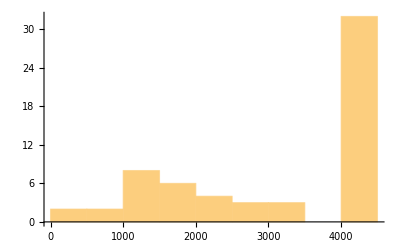

```mathematica
Histogram[tempHistoData,{500}]
```

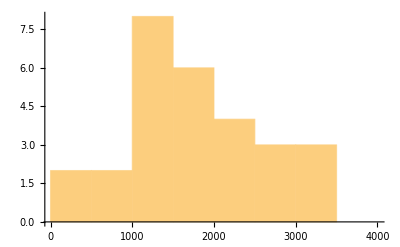

```mathematica
Histogram[Select[tempHistoData, #<4000&],{500},PlotRange->{{0,4000},All}]
```

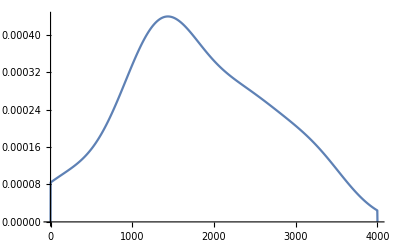

```mathematica
SmoothHistogram[Select[tempHistoData, #<4000&],PlotRange->{{0,4000},All}]
```

## Extracting trial latencies: PP2TrialEscapeLatency(*/PP2TrialResponseLatencyList*)

```mathematica
testDataTrials[[1]]
```

<|TrialNumber→1,STATEDATA→{{STATE,0,21,21,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,4925,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,51182,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,79973,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,99263,3,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,120476,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,144788,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,168337,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,180016,9,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{STATE,0,180093,77,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,0,181015,8,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,0,186082,65,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{STATE,0,187085,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,0,191295,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,203},{STATE,0,191307,12,1,14,FALSE,TRUE,FALSE,FALSE,484,0,203}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    77},{ERROR,99999,Run loop diff is >25 ms:    65},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}|>

```mathematica
(*This way, you only have to deal with one trial worth of state annotations at a time!*)
```

```mathematica
testDataTrials[[1, "STATEDATA"]]
```

{{STATE,0,21,21,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,4925,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,51182,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,79973,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,99263,3,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,120476,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,144788,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,168337,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,180016,9,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{STATE,0,180093,77,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,0,181015,8,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,0,186082,65,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{STATE,0,187085,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,0,191295,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,203},{STATE,0,191307,12,1,14,FALSE,TRUE,FALSE,FALSE,484,0,203}}

```mathematica
SequenceCases[testDataTrials[[1, "STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{7,9}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{7,14,9,14}, state2],___ }
}
]
```

{{{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0}}}

```mathematica
(*Hit trial has no escape*)
SequenceCases[testDataTrials[[2, "STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{7,9}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{7,14,9,14}, state2],___ }
}
]
```

{}

### Paste together into real function

```mathematica
PP2TrialEscapeLatency[trialData_Association]:= 
Module[{tempret},
tempret=SequenceCases[trialData[["STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{7,9}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{7,14,9,14}, state2],___ }
}
];
Switch[Length[tempret],
0, 0(*Null*),
1,tempret[[1, 2, 3]]-tempret[[1, 1, 3]],
_, Message[PP2TrialResponseLatency::trialError, trialData]
]
];
```

```mathematica
PP2TrialEscapeLatency::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialEscapeLatency[x___]:= Message[PP2TrialEscapeLatency::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialEscapeLatency[testDataTrials[[1]]]
```

199

```mathematica
PP2TrialEscapeLatency[testDataTrials[[3]]]
```

0

```mathematica
tempHistoData=PP2TrialEscapeLatency /@ testDataTrials
```

{199,0,0,0,0,0,0,0,0,3003,0,0,305,0,0,668,0,0,0,2605,0,0,0,6002,0,607,0,0,0,0,0,0,0,3028,0,0,5802,4175,0,364,0,0,2029,3321,0,758,440,4013,0,0,476,1227,0,0,0,0,571,0,0,2916}

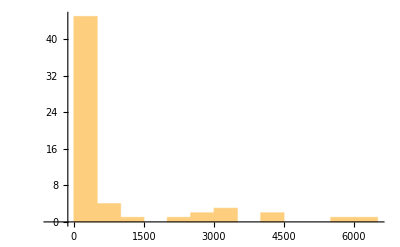

```mathematica
Histogram[tempHistoData,{500}]
```

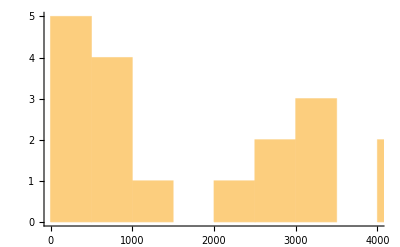

```mathematica
Histogram[Select[tempHistoData, 0<#&],{500},PlotRange->{{0,4000},All}]
```

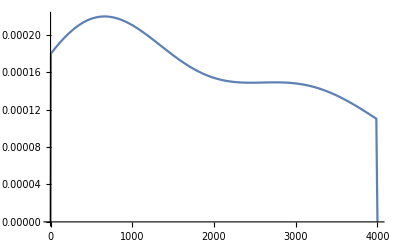

```mathematica
SmoothHistogram[Select[tempHistoData, 0<#&],PlotRange->{{0,4000},All}]
```

## Counting Up the Results

```mathematica
counts=Counts[PP2TrialExtractOutcome /@ testDataTrials ]
```

<|M→11,H→19,CR→21,FA→9|>

```mathematica
{N[counts[["H"]]/(counts[["H"]]+counts[["M"]])],N[counts[["FA"]]/(counts[["CR"]]+counts[["FA"]])]}
```

{0.633333,0.3}